# Order parameters and χ4 for p0=3.75

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/localTest/2DmeltingPhase/N4096/";
```

```mathematica
Tlist={0.063 ,0.039, 0.03105 ,0.025 ,0.016 ,0.01, 0.008 ,0.0063 ,0.005 ,0.00385, 0.0031, 0.0028 ,0.0025, 0.0022 ,0.002};
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000}

```mathematica
orientation=Table[Import[StringJoin[saveFolder,"orientationReIm_N4096_p3.750_T",Tstring[[T]],"_0.nc"],"Data"][[1]],{T,Length[Tlist]}];
```

```mathematica
translation=Table[Import[StringJoin[saveFolder,"timeTranslation_N4096_p3.750_T",Tstring[[T]],"_0.nc"],"Data"][[2]],{T,Length[Tlist]}];
```

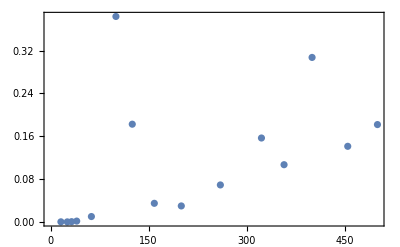

```mathematica
ListPlot[Table[{1/Tlist[[T]],Abs[Mean[Normal[orientation[[T]]]]]},{T,Length[Tlist]}]]
```

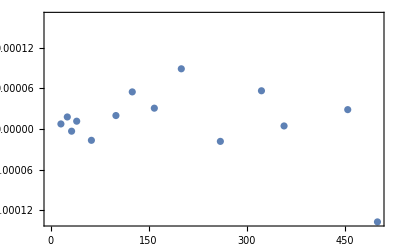

```mathematica
ListPlot[Table[{1/Tlist[[T]],Mean[Normal[translation[[T]]]]},{T,Length[Tlist]}]]
```

```mathematica
4096*Variance[Normal[orientation[[15]]]]
```

0.649575

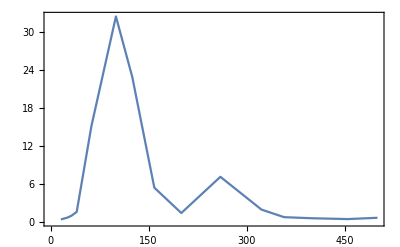

```mathematica
ListPlot[Table[{1/Tlist[[T]],4096*Variance[Normal[orientation[[T]]]]},{T,Length[Tlist]}],Joined->True]
```

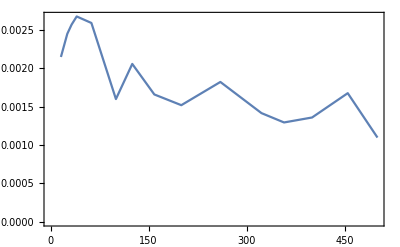

```mathematica
ListPlot[Table[{1/Tlist[[T]],4096*Variance[Normal[translation[[T]]]]},{T,Length[Tlist]}],Joined->True]
```